```mathematica
Solve[-f/(6+2 f) μ^3-3/(6+2 f) μ+1/2-q==0,μ]
```

{{μ→(3 2^(1/3))/((-81 f^2-27 f^3+162 f^2 q+54 f^3 q+√(2916 f^3+(-81 f^2-27 f^3+162 f^2 q+54 f^3 q)^2))^(1/3))-((-81 f^2-27 f^3+162 f^2 q+54 f^3 q+√(2916 f^3+(-81 f^2-27 f^3+162 f^2 q+54 f^3 q)^2))^(1/3))/(3 2^(1/3) f)},{μ→-(3 (1+ⅈ √3))/(2^(2/3) (-81 f^2-27 f^3+162 f^2 q+54 f^3 q+√(2916 f^3+(-81 f^2-27 f^3+162 f^2 q+54 f^3 q)^2))^(1/3))+1/(6 2^(1/3) f)(1-ⅈ √3) (-81 f^2-27 f^3+162 f^2 q+54 f^3 q+√(2916 f^3+(-81 f^2-27 f^3+162 f^2 q+54 f^3 q)^2))^(1/3)},{μ→-(3 (1-ⅈ √3))/(2^(2/3) (-81 f^2-27 f^3+162 f^2 q+54 f^3 q+√(2916 f^3+(-81 f^2-27 f^3+162 f^2 q+54 f^3 q)^2))^(1/3))+1/(6 2^(1/3) f)(1+ⅈ √3) (-81 f^2-27 f^3+162 f^2 q+54 f^3 q+√(2916 f^3+(-81 f^2-27 f^3+162 f^2 q+54 f^3 q)^2))^(1/3)}}

```mathematica
f=0.835;
```

```mathematica
mu[q_]=(2 2^(1/3) f-2^(2/3) (√(f^3 (4+f (3+f)^2 (1-2 q)^2))+f^2 (3+f) (-1+2 q))^(2/3))/(2 f (√(f^3 (4+f (3+f)^2 (1-2 q)^2))+f^2 (3+f) (-1+2 q))^(1/3));
```

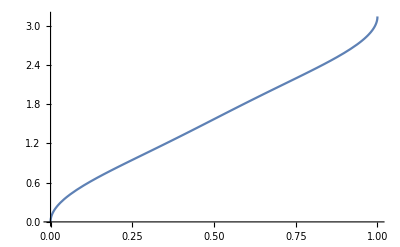

```mathematica
Plot[ArcCos[mu[q]],{q,0,1}]
```

```mathematica
Clear[f];
```

```mathematica
FullSimplify[(3 2^(1/3))/((-81 f^2-27 f^3+162 f^2 q+54 f^3 q+√(2916 f^3+(-81 f^2-27 f^3+162 f^2 q+54 f^3 q)^2))^(1/3))-((-81 f^2-27 f^3+162 f^2 q+54 f^3 q+√(2916 f^3+(-81 f^2-27 f^3+162 f^2 q+54 f^3 q)^2))^(1/3))/(3 2^(1/3) f)]
```

(2 2^(1/3) f-2^(2/3) (√(f^3 (4+f (3+f)^2 (1-2 q)^2))+f^2 (3+f) (-1+2 q))^(2/3))/(2 f (√(f^3 (4+f (3+f)^2 (1-2 q)^2))+f^2 (3+f) (-1+2 q))^(1/3))

```mathematica
Solve[1/((1-δ) δ^v) ((1-δ^(v+1))-3 (n-1)^2/4 δ (1-δ^v))-q==0,δ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-q+(δ^-v (1-δ^(1+v)-3/4 (-1+n)^2 δ (1-δ^v)))/(1-δ)==0,δ]